## Assignment 1

Due Friday Oct. 10 at 4:50 pm

9.2.4

(4) Find tanh(50)-1 to 10 significant figures.

### solution

This does not work:

```mathematica
N[Tanh[50]-1]
```

0.

This does work:

```mathematica
N[Tanh[50]-1,10]
```

-7.440151952×10^-44

9.5.4

(4)  Find the nullspace for the following matrix:  (18 | 6 | 12
6 | 2 | 4
12 | 4 | 8).

Show directly that any vector in the nullspace yields zero when multiplied by the matrix.

### solution

```mathematica
m={{18,6,12},{6,2,4},{12,4,8}};
```

```mathematica
e=NullSpace[m]
```

{{-2,0,3},{-1,3,0}}

Any linear combination of these vectors is in the nullspace:

```mathematica
m.(c1 e[[1]]+ c2 e[[2]])//Expand
```

{0,0,0}

9.5.5(a)

(5) Solve the matrix problem  A·x=u for the unknown vector x,  where

(a)  A=(-1 | 1
3 | 2) and u=(3,1);

### solution

```mathematica
A={{-1,1},{3,2}};
u={3,1};
```

```mathematica
x=Inverse[A].u
```

{-1,2}

or

```mathematica
x={x1,x2};
```

```mathematica
Solve[A.x==u,x]
```

{{x1→-1,x2→2}}

9.6.1

(1) Using a plot, determine whether the equation 3 x^8-2x+1=0  has any real solutions. (Hint: Plot the left-hand side as a function of x and see whether it can equal zero for any real x.)

### solution

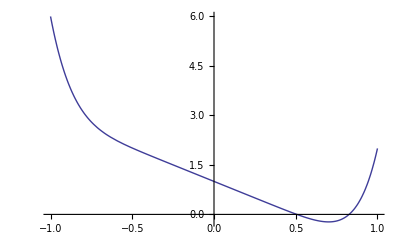

```mathematica
Plot[3 x^8 - 2x + 1==0,{x,-1,1}]
```

From the plot, there are two real solutions at about x = 0.5 and x = 0.82.

9.8.3

(3) Simplify the following equation using Mathematica, and use the result to find all real and complex solutions by hand:

1/30+4/(21 (3 z-1))-3/(26 (2 z+1))-41/(455 (5 z-4))=0.

### solution

```mathematica
1/30+4/(21 (3 z-1))-3/(26 (2 z+1))-41/(455 (5 z-4))//FullSimplify
```

((-1+z) (1+z^2))/((1+2 z) (-1+3 z) (-4+5 z))

The numerator is zero at z=1 and at z^2=-1, which implies z=ⅈ and z=-ⅈ.

9.8.5(d)

(5) Define the following functions and, if asked,  plot them over the given range of values:

(d) f(x) = Piecewise[{{x,, x<0}, {x^2,
1/x^2,, 0≤ x≤ 1
x>1}}]      Plot for -3<x<3.

### solution

```mathematica
f[x_] = Piecewise[{{x,x<0},{x^2,0<+ x≤ 1},{1/x^2,x>1}}]
```

Piecewise[{{x, x<0}, {x^2, 0<x≤1}, {1/x^2, x>1}, {0, True}}]

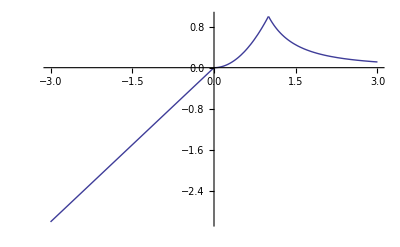

```mathematica
Plot[f[x],{x,-3,3}]
```

or

```mathematica
Clear[f];
```

```mathematica
f[x_] := x/; x<0
f[x_] := x^2 /; 0≤ x≤ 1
f[x_] := 1/x^2 /; x>1
```

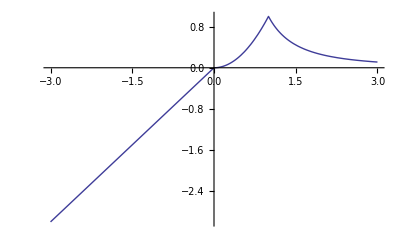

```mathematica
Plot[f[x],{x,-3,3}]
```

9.9.2

(2) Find all local extrema of the following function of x and y, and classify these extrema as either minima, maxima or saddlepoints: 
			 f(x,y)=y x^2+y^2 x-2 x(y+2).

Find the value of the function at each extremum. (Hint: A high-resolution contour plot is helpful. )

### solution

```mathematica
Clear["Global`*"]
```

```mathematica
f[x_,y_] = y x^2 + y^2 x -2x(y+2);
```

```mathematica
d1=D[f[x,y],x]//Factor
```

-4-2 y+2 x y+y^2

```mathematica
d2=D[f[x,y],y]//Factor
```

x (-2+x+2 y)

Plot where the expressions d1 and d2 are equal to zero using a contour plot:

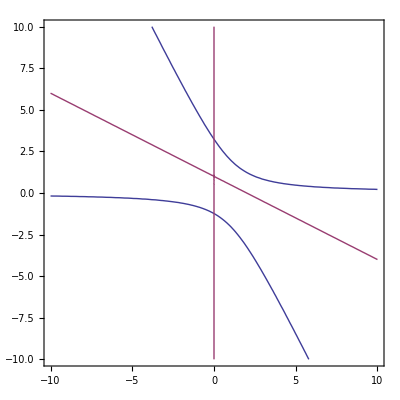

```mathematica
cp=ContourPlot[{d1,d2},{x,-10,10},{y,-10,10},Contours->{0},PlotPoints->20,ContourShading->False]
```

Where the lines cross there is an extremum. The extrema are at x=0.

```mathematica
d1/.x->0
```

-4-2 y+y^2

The solution to d1 = 0 can then be found using the usual rule for a quadratic:

```mathematica
y1=1 + Sqrt[1+4]; y2 = 1 - Sqrt[1 + 4];
```

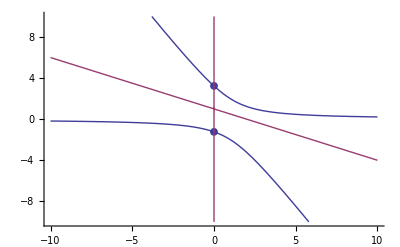

```mathematica
ListPlot[{{0,y1},{0,y2}},PlotStyle->PointSize[0.014]];
Show[%,cp]
```

So extrema are at (0,1 ± 5).

To classify the extrema, use a contour plot of f(x,y):

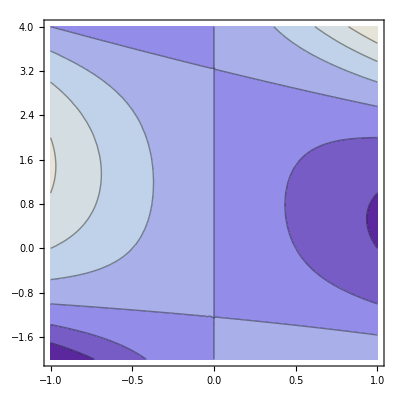

```mathematica
ContourPlot[f[x,y],{x,-1,1},{y,-2,4}]
```

Both extrema are saddle points.

9.9.5

(5) Find the power series expansion to 6th order around x=0 of the function f(x)=(x+1)ln(x+1) . Plot the resulting series on the same graph as f(x) for -1<x<2. Repeat for the 100th-order series. Can you tell from these plots what is the radius of convergence of this power series?

### solution

```mathematica
Clear["Global`*"]
```

```mathematica
f[x_] = (x+1) Log[x+1];
```

```mathematica
Series[f[x],{x,0,6}]
```

x+x^2/2-x^3/6+x^4/12-x^5/20+x^6/30+O[x]^7

```mathematica
s = Normal[%];
```

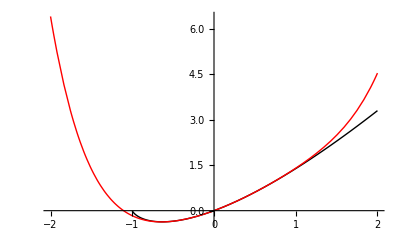

```mathematica
pl=Plot[{f[x],s},{x,-2,2},PlotStyle->{RGBColor[0,0,0],RGBColor[1,0,0]}]
```

```mathematica
Series[f[x],{x,0,30}];
```

```mathematica
s = Normal[%];
```

```mathematica
Plot[{f[x],s},{x,-1.5,1.5},PlotStyle->{RGBColor[0,0,0],RGBColor[0,1,0]},PlotRange->{-1,10}];
```

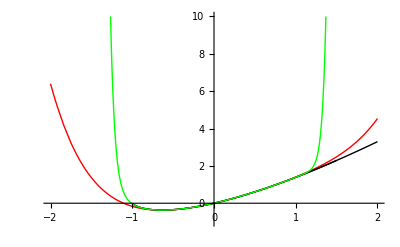

```mathematica
Show[pl,%,PlotRange->{-1,10}]
```

Looks like ther series is breaking down near x=+-1, so estimate radius of convergence is 1.

9.10.3

(3) Solve the following coupled equations analytically, finding all solutions (real and complex):

x^2+2 y=0,

y^2+2 x=0

Find numerical values for the solutions.

### solution

```mathematica
Clear["Global`*"]
```

```mathematica
equations={x^2 +2y==0,y^2 + 2x==0};
```

```mathematica
Solve[equations,{x,y}]
```

{{x→-2,y→-2},{x→0,y→0},{x→2 (-1)^(1/3),y→-2 (-1)^(2/3)},{x→-2 (-1)^(2/3),y→2 (-1)^(1/3)}}

```mathematica
N[%]
```

{{x→-2.,y→-2.},{x→0.,y→0.},{x→1.+1.73205 ⅈ,y→1.-1.73205 ⅈ},{x→1.-1.73205 ⅈ,y→1.+1.73205 ⅈ}}

There are 4 sets of solutions to the equations (2 real and 2 complex).

9.11.10

(10) In this exercise we will derive our own cubic spline interpolation algorithm. As described in Sec. 9.11.3, we require a sequence of  third-order polynomials p_j(x) = ∑_(i=0)^3 c_(j i)x^i, j=1,...M-1, chosen to pass through a set of data {x_j, y_j}, j=1,...,M, where the x_j's are ordered consecutively from lowest to highest values as j increases. Each polynomial p_j(x) in the set is used only between grid points x_j  and x_(j+1), and is chosen so that the first and second derivatives match those of neighboring polynomials at their common grid points, so that the interpolating function is continuous and has continuous first and second derivatives. Thus, the polynomials satisfy the following linear equations:

p_j(x_j)=y_j, j=1,...M-1,
p_j(x_(j+1))=y_(j+1), j=1,...M-1,
p_j'(x_(j+1))=p_(j+1)'(x_(j+1)), j=1,...M-2,
p_j''(x_(j+1))=p_(j+1)''(x_(j+1)), j=1,...M-2.

These 4M-6 equations are almost enough to uniquely specify the 4(M-1) coefficients c_(j i) in the M-1 polynomials p_j(x), but we need two more equations. Typically, one chooses that the second derivative vanish at each end, providing the equations

p_1''(x_1)=p_(M-1)''(x_M)=0.

(a) Using Solve, set up and solve these coupled linear equations for the c_(j i), given the data defined in Cell 9.188.

```mathematica
data=Table[{x,x^5},{x,-1,1,0.05}];
f=Interpolation[data]
```

InterpolatingFunction[{{-1.,1.}},<>]

(b) The following interpolation function will evaluate the spline for any value of x chosen between x_1  and x_M, given that each polynomial p_j(x) has been defined as a Mathematica function p[j,x]. Here, the solution from Solve is assumed to be a simple list of substitution commands for the c_(j i)'s called sol.

```mathematica
finterp[x_,data_] := (M=Length[data]; j1 = 1; jM=M; While[jM-j1>1,jav=Floor[(jM+j1)/2];If[data[[jav,1]]>x, jM=jav,j1=jav]]; p[j1,x]) /.sol
```

This interpolation function must find the correct polynomial p_j associated with a given x: it corresponds to the x_j value in the data set nearest to but less than x. We use a division method, recursively dividing the data in half and testing which half x falls in, until x falls between consecutive grid points. (A faster method is possible if the grid points are evenly spaced, with spacing Δx. Then j= Min[Floor[(x-x_1)/Δx] + 1, M]. ) We have also employed an If statement and a While statement.  An If statement takes three arguments. The first argument is a condition which, if met, returns the second argument. If the condition evaluates to False, the third argument is returned. In While statements the second argument is evaluated over and over again as long as the test corresponding to the first argument evaluates to True. (The second argument can be several commands separated by semicolons, as in the above example. )
Use this function to plot the spline interpolation found in part (a) in the range -1≤ x≤ 1.

### solution

#### (a)

Equations to be solved:

p_j(x_j)=y_j, j=1,...M-1,
p_j(x_(j+1))=y_(j+1), j=1,...M-1,
p_j'(x_(j+1))=p_(j+1)'(x_(j+1)), j=1,...M-2,
p_j''(x_(j+1))=p_(j+1)''(x_(j+1)), j=1,...M-2.

p_1''(x_1)=p_(M-1)''(x_M)=0.

```mathematica
Clear["Global`*"]
```

```mathematica
data=Table[{x,x^5},{x,-1,1,0.05}];
```

```mathematica
M=Length[data]
```

41

Define x and y values in the data set:

```mathematica
y[j_]:= data[[j,2]]/; j∈Integers && 1≤ j≤ M;
x[j_]:= data[[j,1]]/; j∈Integers && 1≤ j≤ M;
```

Define the polynomial with coefficients c[j,i] to be determined:

```mathematica
p[j_,x_]= Sum[c[j,i] x^i,{i,0,3}]
```

c[j,0]+x c[j,1]+x^2 c[j,2]+x^3 c[j,3]

Set up the equations:

```mathematica
eq1=Table[{p[j,x[j]]==y[j],p[j,x[j+1]]==y[j+1]},{j,1,M-1}]//Flatten
```

{c[1,0]-1. c[1,1]+1. c[1,2]-1. c[1,3]==-1.,c[1,0]-0.95 c[1,1]+0.9025 c[1,2]-0.857375 c[1,3]==-0.773781,c[2,0]-0.95 c[2,1]+0.9025 c[2,2]-0.857375 c[2,3]==-0.773781,c[2,0]-0.9 c[2,1]+0.81 c[2,2]-0.729 c[2,3]==-0.59049,c[3,0]-0.9 c[3,1]+0.81 c[3,2]-0.729 c[3,3]==-0.59049,c[3,0]-0.85 c[3,1]+0.7225 c[3,2]-0.614125 c[3,3]==-0.443705,c[4,0]-0.85 c[4,1]+0.7225 c[4,2]-0.614125 c[4,3]==-0.443705,c[4,0]-0.8 c[4,1]+0.64 c[4,2]-0.512 c[4,3]==-0.32768,c[5,0]-0.8 c[5,1]+0.64 c[5,2]-0.512 c[5,3]==-0.32768,c[5,0]-0.75 c[5,1]+0.5625 c[5,2]-0.421875 c[5,3]==-0.237305,c[6,0]-0.75 c[6,1]+0.5625 c[6,2]-0.421875 c[6,3]==-0.237305,c[6,0]-0.7 c[6,1]+0.49 c[6,2]-0.343 c[6,3]==-0.16807,c[7,0]-0.7 c[7,1]+0.49 c[7,2]-0.343 c[7,3]==-0.16807,c[7,0]-0.65 c[7,1]+0.4225 c[7,2]-0.274625 c[7,3]==-0.116029,c[8,0]-0.65 c[8,1]+0.4225 c[8,2]-0.274625 c[8,3]==-0.116029,c[8,0]-0.6 c[8,1]+0.36 c[8,2]-0.216 c[8,3]==-0.07776,c[9,0]-0.6 c[9,1]+0.36 c[9,2]-0.216 c[9,3]==-0.07776,c[9,0]-0.55 c[9,1]+0.3025 c[9,2]-0.166375 c[9,3]==-0.0503284,c[10,0]-0.55 c[10,1]+0.3025 c[10,2]-0.166375 c[10,3]==-0.0503284,c[10,0]-0.5 c[10,1]+0.25 c[10,2]-0.125 c[10,3]==-0.03125,c[11,0]-0.5 c[11,1]+0.25 c[11,2]-0.125 c[11,3]==-0.03125,c[11,0]-0.45 c[11,1]+0.2025 c[11,2]-0.091125 c[11,3]==-0.0184528,c[12,0]-0.45 c[12,1]+0.2025 c[12,2]-0.091125 c[12,3]==-0.0184528,c[12,0]-0.4 c[12,1]+0.16 c[12,2]-0.064 c[12,3]==-0.01024,c[13,0]-0.4 c[13,1]+0.16 c[13,2]-0.064 c[13,3]==-0.01024,c[13,0]-0.35 c[13,1]+0.1225 c[13,2]-0.042875 c[13,3]==-0.00525219,c[14,0]-0.35 c[14,1]+0.1225 c[14,2]-0.042875 c[14,3]==-0.00525219,c[14,0]-0.3 c[14,1]+0.09 c[14,2]-0.027 c[14,3]==-0.00243,c[15,0]-0.3 c[15,1]+0.09 c[15,2]-0.027 c[15,3]==-0.00243,c[15,0]-0.25 c[15,1]+0.0625 c[15,2]-0.015625 c[15,3]==-0.000976563,c[16,0]-0.25 c[16,1]+0.0625 c[16,2]-0.015625 c[16,3]==-0.000976563,c[16,0]-0.2 c[16,1]+0.04 c[16,2]-0.008 c[16,3]==-0.00032,c[17,0]-0.2 c[17,1]+0.04 c[17,2]-0.008 c[17,3]==-0.00032,c[17,0]-0.15 c[17,1]+0.0225 c[17,2]-0.003375 c[17,3]==-0.0000759375,c[18,0]-0.15 c[18,1]+0.0225 c[18,2]-0.003375 c[18,3]==-0.0000759375,c[18,0]-0.1 c[18,1]+0.01 c[18,2]-0.001 c[18,3]==-0.00001,c[19,0]-0.1 c[19,1]+0.01 c[19,2]-0.001 c[19,3]==-0.00001,c[19,0]-0.05 c[19,1]+0.0025 c[19,2]-0.000125 c[19,3]==-3.125×10^-7,c[20,0]-0.05 c[20,1]+0.0025 c[20,2]-0.000125 c[20,3]==-3.125×10^-7,0.+c[20,0]==0.,0.+c[21,0]==0.,c[21,0]+0.05 c[21,1]+0.0025 c[21,2]+0.000125 c[21,3]==3.125×10^-7,c[22,0]+0.05 c[22,1]+0.0025 c[22,2]+0.000125 c[22,3]==3.125×10^-7,c[22,0]+0.1 c[22,1]+0.01 c[22,2]+0.001 c[22,3]==0.00001,c[23,0]+0.1 c[23,1]+0.01 c[23,2]+0.001 c[23,3]==0.00001,c[23,0]+0.15 c[23,1]+0.0225 c[23,2]+0.003375 c[23,3]==0.0000759375,c[24,0]+0.15 c[24,1]+0.0225 c[24,2]+0.003375 c[24,3]==0.0000759375,c[24,0]+0.2 c[24,1]+0.04 c[24,2]+0.008 c[24,3]==0.00032,c[25,0]+0.2 c[25,1]+0.04 c[25,2]+0.008 c[25,3]==0.00032,c[25,0]+0.25 c[25,1]+0.0625 c[25,2]+0.015625 c[25,3]==0.000976563,c[26,0]+0.25 c[26,1]+0.0625 c[26,2]+0.015625 c[26,3]==0.000976563,c[26,0]+0.3 c[26,1]+0.09 c[26,2]+0.027 c[26,3]==0.00243,c[27,0]+0.3 c[27,1]+0.09 c[27,2]+0.027 c[27,3]==0.00243,c[27,0]+0.35 c[27,1]+0.1225 c[27,2]+0.042875 c[27,3]==0.00525219,c[28,0]+0.35 c[28,1]+0.1225 c[28,2]+0.042875 c[28,3]==0.00525219,c[28,0]+0.4 c[28,1]+0.16 c[28,2]+0.064 c[28,3]==0.01024,c[29,0]+0.4 c[29,1]+0.16 c[29,2]+0.064 c[29,3]==0.01024,c[29,0]+0.45 c[29,1]+0.2025 c[29,2]+0.091125 c[29,3]==0.0184528,c[30,0]+0.45 c[30,1]+0.2025 c[30,2]+0.091125 c[30,3]==0.0184528,c[30,0]+0.5 c[30,1]+0.25 c[30,2]+0.125 c[30,3]==0.03125,c[31,0]+0.5 c[31,1]+0.25 c[31,2]+0.125 c[31,3]==0.03125,c[31,0]+0.55 c[31,1]+0.3025 c[31,2]+0.166375 c[31,3]==0.0503284,c[32,0]+0.55 c[32,1]+0.3025 c[32,2]+0.166375 c[32,3]==0.0503284,c[32,0]+0.6 c[32,1]+0.36 c[32,2]+0.216 c[32,3]==0.07776,c[33,0]+0.6 c[33,1]+0.36 c[33,2]+0.216 c[33,3]==0.07776,c[33,0]+0.65 c[33,1]+0.4225 c[33,2]+0.274625 c[33,3]==0.116029,c[34,0]+0.65 c[34,1]+0.4225 c[34,2]+0.274625 c[34,3]==0.116029,c[34,0]+0.7 c[34,1]+0.49 c[34,2]+0.343 c[34,3]==0.16807,c[35,0]+0.7 c[35,1]+0.49 c[35,2]+0.343 c[35,3]==0.16807,c[35,0]+0.75 c[35,1]+0.5625 c[35,2]+0.421875 c[35,3]==0.237305,c[36,0]+0.75 c[36,1]+0.5625 c[36,2]+0.421875 c[36,3]==0.237305,c[36,0]+0.8 c[36,1]+0.64 c[36,2]+0.512 c[36,3]==0.32768,c[37,0]+0.8 c[37,1]+0.64 c[37,2]+0.512 c[37,3]==0.32768,c[37,0]+0.85 c[37,1]+0.7225 c[37,2]+0.614125 c[37,3]==0.443705,c[38,0]+0.85 c[38,1]+0.7225 c[38,2]+0.614125 c[38,3]==0.443705,c[38,0]+0.9 c[38,1]+0.81 c[38,2]+0.729 c[38,3]==0.59049,c[39,0]+0.9 c[39,1]+0.81 c[39,2]+0.729 c[39,3]==0.59049,c[39,0]+0.95 c[39,1]+0.9025 c[39,2]+0.857375 c[39,3]==0.773781,c[40,0]+0.95 c[40,1]+0.9025 c[40,2]+0.857375 c[40,3]==0.773781,c[40,0]+1. c[40,1]+1. c[40,2]+1. c[40,3]==1.}

```mathematica
eq2=Table[
   {D[p[j,x],x]==D[p[j+1,x],x],
D[p[j,x],{x,2}]==D[p[j+1,x],{x,2}]}/.x->x[j+1],{j,1,M-2}]//Flatten
```

{c[1,1]-1.9 c[1,2]+2.7075 c[1,3]==c[2,1]-1.9 c[2,2]+2.7075 c[2,3],2 c[1,2]-5.7 c[1,3]==2 c[2,2]-5.7 c[2,3],c[2,1]-1.8 c[2,2]+2.43 c[2,3]==c[3,1]-1.8 c[3,2]+2.43 c[3,3],2 c[2,2]-5.4 c[2,3]==2 c[3,2]-5.4 c[3,3],c[3,1]-1.7 c[3,2]+2.1675 c[3,3]==c[4,1]-1.7 c[4,2]+2.1675 c[4,3],2 c[3,2]-5.1 c[3,3]==2 c[4,2]-5.1 c[4,3],c[4,1]-1.6 c[4,2]+1.92 c[4,3]==c[5,1]-1.6 c[5,2]+1.92 c[5,3],2 c[4,2]-4.8 c[4,3]==2 c[5,2]-4.8 c[5,3],c[5,1]-1.5 c[5,2]+1.6875 c[5,3]==c[6,1]-1.5 c[6,2]+1.6875 c[6,3],2 c[5,2]-4.5 c[5,3]==2 c[6,2]-4.5 c[6,3],c[6,1]-1.4 c[6,2]+1.47 c[6,3]==c[7,1]-1.4 c[7,2]+1.47 c[7,3],2 c[6,2]-4.2 c[6,3]==2 c[7,2]-4.2 c[7,3],c[7,1]-1.3 c[7,2]+1.2675 c[7,3]==c[8,1]-1.3 c[8,2]+1.2675 c[8,3],2 c[7,2]-3.9 c[7,3]==2 c[8,2]-3.9 c[8,3],c[8,1]-1.2 c[8,2]+1.08 c[8,3]==c[9,1]-1.2 c[9,2]+1.08 c[9,3],2 c[8,2]-3.6 c[8,3]==2 c[9,2]-3.6 c[9,3],c[9,1]-1.1 c[9,2]+0.9075 c[9,3]==c[10,1]-1.1 c[10,2]+0.9075 c[10,3],2 c[9,2]-3.3 c[9,3]==2 c[10,2]-3.3 c[10,3],c[10,1]-1. c[10,2]+0.75 c[10,3]==c[11,1]-1. c[11,2]+0.75 c[11,3],2 c[10,2]-3. c[10,3]==2 c[11,2]-3. c[11,3],c[11,1]-0.9 c[11,2]+0.6075 c[11,3]==c[12,1]-0.9 c[12,2]+0.6075 c[12,3],2 c[11,2]-2.7 c[11,3]==2 c[12,2]-2.7 c[12,3],c[12,1]-0.8 c[12,2]+0.48 c[12,3]==c[13,1]-0.8 c[13,2]+0.48 c[13,3],2 c[12,2]-2.4 c[12,3]==2 c[13,2]-2.4 c[13,3],c[13,1]-0.7 c[13,2]+0.3675 c[13,3]==c[14,1]-0.7 c[14,2]+0.3675 c[14,3],2 c[13,2]-2.1 c[13,3]==2 c[14,2]-2.1 c[14,3],c[14,1]-0.6 c[14,2]+0.27 c[14,3]==c[15,1]-0.6 c[15,2]+0.27 c[15,3],2 c[14,2]-1.8 c[14,3]==2 c[15,2]-1.8 c[15,3],c[15,1]-0.5 c[15,2]+0.1875 c[15,3]==c[16,1]-0.5 c[16,2]+0.1875 c[16,3],2 c[15,2]-1.5 c[15,3]==2 c[16,2]-1.5 c[16,3],c[16,1]-0.4 c[16,2]+0.12 c[16,3]==c[17,1]-0.4 c[17,2]+0.12 c[17,3],2 c[16,2]-1.2 c[16,3]==2 c[17,2]-1.2 c[17,3],c[17,1]-0.3 c[17,2]+0.0675 c[17,3]==c[18,1]-0.3 c[18,2]+0.0675 c[18,3],2 c[17,2]-0.9 c[17,3]==2 c[18,2]-0.9 c[18,3],c[18,1]-0.2 c[18,2]+0.03 c[18,3]==c[19,1]-0.2 c[19,2]+0.03 c[19,3],2 c[18,2]-0.6 c[18,3]==2 c[19,2]-0.6 c[19,3],c[19,1]-0.1 c[19,2]+0.0075 c[19,3]==c[20,1]-0.1 c[20,2]+0.0075 c[20,3],2 c[19,2]-0.3 c[19,3]==2 c[20,2]-0.3 c[20,3],0.+c[20,1]==0.+c[21,1],0.+2 c[20,2]==0.+2 c[21,2],c[21,1]+0.1 c[21,2]+0.0075 c[21,3]==c[22,1]+0.1 c[22,2]+0.0075 c[22,3],2 c[21,2]+0.3 c[21,3]==2 c[22,2]+0.3 c[22,3],c[22,1]+0.2 c[22,2]+0.03 c[22,3]==c[23,1]+0.2 c[23,2]+0.03 c[23,3],2 c[22,2]+0.6 c[22,3]==2 c[23,2]+0.6 c[23,3],c[23,1]+0.3 c[23,2]+0.0675 c[23,3]==c[24,1]+0.3 c[24,2]+0.0675 c[24,3],2 c[23,2]+0.9 c[23,3]==2 c[24,2]+0.9 c[24,3],c[24,1]+0.4 c[24,2]+0.12 c[24,3]==c[25,1]+0.4 c[25,2]+0.12 c[25,3],2 c[24,2]+1.2 c[24,3]==2 c[25,2]+1.2 c[25,3],c[25,1]+0.5 c[25,2]+0.1875 c[25,3]==c[26,1]+0.5 c[26,2]+0.1875 c[26,3],2 c[25,2]+1.5 c[25,3]==2 c[26,2]+1.5 c[26,3],c[26,1]+0.6 c[26,2]+0.27 c[26,3]==c[27,1]+0.6 c[27,2]+0.27 c[27,3],2 c[26,2]+1.8 c[26,3]==2 c[27,2]+1.8 c[27,3],c[27,1]+0.7 c[27,2]+0.3675 c[27,3]==c[28,1]+0.7 c[28,2]+0.3675 c[28,3],2 c[27,2]+2.1 c[27,3]==2 c[28,2]+2.1 c[28,3],c[28,1]+0.8 c[28,2]+0.48 c[28,3]==c[29,1]+0.8 c[29,2]+0.48 c[29,3],2 c[28,2]+2.4 c[28,3]==2 c[29,2]+2.4 c[29,3],c[29,1]+0.9 c[29,2]+0.6075 c[29,3]==c[30,1]+0.9 c[30,2]+0.6075 c[30,3],2 c[29,2]+2.7 c[29,3]==2 c[30,2]+2.7 c[30,3],c[30,1]+1. c[30,2]+0.75 c[30,3]==c[31,1]+1. c[31,2]+0.75 c[31,3],2 c[30,2]+3. c[30,3]==2 c[31,2]+3. c[31,3],c[31,1]+1.1 c[31,2]+0.9075 c[31,3]==c[32,1]+1.1 c[32,2]+0.9075 c[32,3],2 c[31,2]+3.3 c[31,3]==2 c[32,2]+3.3 c[32,3],c[32,1]+1.2 c[32,2]+1.08 c[32,3]==c[33,1]+1.2 c[33,2]+1.08 c[33,3],2 c[32,2]+3.6 c[32,3]==2 c[33,2]+3.6 c[33,3],c[33,1]+1.3 c[33,2]+1.2675 c[33,3]==c[34,1]+1.3 c[34,2]+1.2675 c[34,3],2 c[33,2]+3.9 c[33,3]==2 c[34,2]+3.9 c[34,3],c[34,1]+1.4 c[34,2]+1.47 c[34,3]==c[35,1]+1.4 c[35,2]+1.47 c[35,3],2 c[34,2]+4.2 c[34,3]==2 c[35,2]+4.2 c[35,3],c[35,1]+1.5 c[35,2]+1.6875 c[35,3]==c[36,1]+1.5 c[36,2]+1.6875 c[36,3],2 c[35,2]+4.5 c[35,3]==2 c[36,2]+4.5 c[36,3],c[36,1]+1.6 c[36,2]+1.92 c[36,3]==c[37,1]+1.6 c[37,2]+1.92 c[37,3],2 c[36,2]+4.8 c[36,3]==2 c[37,2]+4.8 c[37,3],c[37,1]+1.7 c[37,2]+2.1675 c[37,3]==c[38,1]+1.7 c[38,2]+2.1675 c[38,3],2 c[37,2]+5.1 c[37,3]==2 c[38,2]+5.1 c[38,3],c[38,1]+1.8 c[38,2]+2.43 c[38,3]==c[39,1]+1.8 c[39,2]+2.43 c[39,3],2 c[38,2]+5.4 c[38,3]==2 c[39,2]+5.4 c[39,3],c[39,1]+1.9 c[39,2]+2.7075 c[39,3]==c[40,1]+1.9 c[40,2]+2.7075 c[40,3],2 c[39,2]+5.7 c[39,3]==2 c[40,2]+5.7 c[40,3]}

```mathematica
eq3={D[p[1,x],{x,2}]==0/.x->x[1],D[p[M-1,x],{x,2}]==0/.x->x[M]}
```

{2 c[1,2]-6. c[1,3]==0,2 c[40,2]+6. c[40,3]==0}

```mathematica
eqs=Join[eq1,eq2,eq3];
```

```mathematica
vars=Table[c[j,i],{j,1,M-1},{i,0,3}]//Flatten
```

{c[1,0],c[1,1],c[1,2],c[1,3],c[2,0],c[2,1],c[2,2],c[2,3],c[3,0],c[3,1],c[3,2],c[3,3],c[4,0],c[4,1],c[4,2],c[4,3],c[5,0],c[5,1],c[5,2],c[5,3],c[6,0],c[6,1],c[6,2],c[6,3],c[7,0],c[7,1],c[7,2],c[7,3],c[8,0],c[8,1],c[8,2],c[8,3],c[9,0],c[9,1],c[9,2],c[9,3],c[10,0],c[10,1],c[10,2],c[10,3],c[11,0],c[11,1],c[11,2],c[11,3],c[12,0],c[12,1],c[12,2],c[12,3],c[13,0],c[13,1],c[13,2],c[13,3],c[14,0],c[14,1],c[14,2],c[14,3],c[15,0],c[15,1],c[15,2],c[15,3],c[16,0],c[16,1],c[16,2],c[16,3],c[17,0],c[17,1],c[17,2],c[17,3],c[18,0],c[18,1],c[18,2],c[18,3],c[19,0],c[19,1],c[19,2],c[19,3],c[20,0],c[20,1],c[20,2],c[20,3],c[21,0],c[21,1],c[21,2],c[21,3],c[22,0],c[22,1],c[22,2],c[22,3],c[23,0],c[23,1],c[23,2],c[23,3],c[24,0],c[24,1],c[24,2],c[24,3],c[25,0],c[25,1],c[25,2],c[25,3],c[26,0],c[26,1],c[26,2],c[26,3],c[27,0],c[27,1],c[27,2],c[27,3],c[28,0],c[28,1],c[28,2],c[28,3],c[29,0],c[29,1],c[29,2],c[29,3],c[30,0],c[30,1],c[30,2],c[30,3],c[31,0],c[31,1],c[31,2],c[31,3],c[32,0],c[32,1],c[32,2],c[32,3],c[33,0],c[33,1],c[33,2],c[33,3],c[34,0],c[34,1],c[34,2],c[34,3],c[35,0],c[35,1],c[35,2],c[35,3],c[36,0],c[36,1],c[36,2],c[36,3],c[37,0],c[37,1],c[37,2],c[37,3],c[38,0],c[38,1],c[38,2],c[38,3],c[39,0],c[39,1],c[39,2],c[39,3],c[40,0],c[40,1],c[40,2],c[40,3]}

Number of equations and unknowns should be the same:

```mathematica
Length[eqs]
```

160

```mathematica
Length[vars]
```

160

```mathematica
sol=Solve[eqs,vars]
```

{{c[1,0]→-71.2084,c[1,1]→-220.049,c[1,2]→-224.76,c[1,3]→-74.9201,c[2,0]→19.7554,c[2,1]→67.2054,c[2,2]→77.6124,c[2,3]→31.1756,c[3,0]→-1.8105,c[3,1]→-4.68078,c[3,2]→-2.26119,c[3,3]→1.59278,c[4,0]→2.38737,c[4,1]→10.1352,c[4,2]→15.1694,c[4,3]→8.42831,c[5,0]→0.923394,c[5,1]→4.64532,c[5,2]→8.30703,c[5,3]→5.56898,c[6,0]→0.839777,c[6,1]→4.31085,c[6,2]→7.86107,c[6,3]→5.37078,c[7,0]→0.548963,c[7,1]→3.06451,c[7,2]→6.08058,c[7,3]→4.52292,c[8,0]→0.381337,c[8,1]→2.29085,c[8,2]→4.89034,c[8,3]→3.91254,c[9,0]→0.249444,c[9,1]→1.63138,c[9,2]→3.79123,c[9,3]→3.30192,c[10,0]→0.158411,c[10,1]→1.13484,c[10,2]→2.88842,c[10,3]→2.75477,c[11,0]→0.0958156,c[11,1]→0.759269,c[11,2]→2.13728,c[11,3]→2.25401,c[12,0]→0.054828,c[12,1]→0.486018,c[12,2]→1.53005,c[12,3]→1.80421,c[13,0]→0.0292245,c[13,1]→0.293991,c[13,2]→1.04999,c[13,3]→1.40416,c[14,0]→0.0142188,c[14,1]→0.165372,c[14,2]→0.682503,c[14,3]→1.05417,c[15,0]→0.00611874,c[15,1]→0.0843707,c[15,2]→0.412499,c[15,3]→0.754166,c[16,0]→0.0022125,c[16,1]→0.0374959,c[16,2]→0.225,c[16,3]→0.504167,c[17,0]→0.0006125,c[17,1]→0.0134958,c[17,2]→0.105,c[17,3]→0.304167,c[18,0]→0.00010625,c[18,1]→0.00337083,c[18,2]→0.0375,c[18,3]→0.154167,c[19,0]→6.25×10^-6,c[19,1]→0.000370833,c[19,2]→0.0075,c[19,3]→0.0541667,c[20,0]→0.,c[20,1]→-4.16667×10^-6,c[20,2]→-9.89622×10^-18,c[20,3]→0.00416667,c[21,0]→0.,c[21,1]→-4.16667×10^-6,c[21,2]→-9.89622×10^-18,c[21,3]→0.00416667,c[22,0]→-6.25×10^-6,c[22,1]→0.000370833,c[22,2]→-0.0075,c[22,3]→0.0541667,c[23,0]→-0.00010625,c[23,1]→0.00337083,c[23,2]→-0.0375,c[23,3]→0.154167,c[24,0]→-0.0006125,c[24,1]→0.0134958,c[24,2]→-0.105,c[24,3]→0.304167,c[25,0]→-0.0022125,c[25,1]→0.0374959,c[25,2]→-0.225,c[25,3]→0.504167,c[26,0]→-0.00611874,c[26,1]→0.0843707,c[26,2]→-0.412499,c[26,3]→0.754166,c[27,0]→-0.0142188,c[27,1]→0.165372,c[27,2]→-0.682503,c[27,3]→1.05417,c[28,0]→-0.0292245,c[28,1]→0.293991,c[28,2]→-1.04999,c[28,3]→1.40416,c[29,0]→-0.054828,c[29,1]→0.486018,c[29,2]→-1.53005,c[29,3]→1.80421,c[30,0]→-0.0958156,c[30,1]→0.759269,c[30,2]→-2.13728,c[30,3]→2.25401,c[31,0]→-0.158411,c[31,1]→1.13484,c[31,2]→-2.88842,c[31,3]→2.75477,c[32,0]→-0.249444,c[32,1]→1.63138,c[32,2]→-3.79123,c[32,3]→3.30192,c[33,0]→-0.381337,c[33,1]→2.29085,c[33,2]→-4.89034,c[33,3]→3.91254,c[34,0]→-0.548963,c[34,1]→3.06451,c[34,2]→-6.08058,c[34,3]→4.52292,c[35,0]→-0.839777,c[35,1]→4.31085,c[35,2]→-7.86107,c[35,3]→5.37078,c[36,0]→-0.923394,c[36,1]→4.64532,c[36,2]→-8.30703,c[36,3]→5.56898,c[37,0]→-2.38737,c[37,1]→10.1352,c[37,2]→-15.1694,c[37,3]→8.42831,c[38,0]→1.8105,c[38,1]→-4.68078,c[38,2]→2.26119,c[38,3]→1.59278,c[39,0]→-19.7554,c[39,1]→67.2054,c[39,2]→-77.6124,c[39,3]→31.1756,c[40,0]→71.2084,c[40,1]→-220.049,c[40,2]→224.76,c[40,3]→-74.9201}}

```mathematica
eqs[[160]]
```

2 c[41,2]+6. c[41,3]==0

#### (b)

```mathematica
finterp[x_,data_] := (M=Length[data]; j1 = 1; jM=M; While[jM-j1>1,jav=Floor[(jM+j1)/2];If[data[[jav,1]]>x, jM=jav,j1=jav]]; p[j1,x]) /.sol[[1]]
```

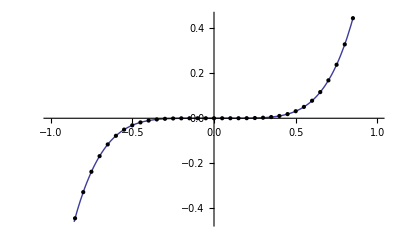

```mathematica
Plot[finterp[x,data],{x,-1,1},Epilog->Point/@data]
```